```mathematica
(*Defining numerical values of system parameters: Tp - load reversal time (seconds), b - white noise amplitude, Tt - turbine time-constant (seconds), H - inertia time-constant (seconds), Ki - secondary control constant (inverse seconds), a - inverse droop of the system, xdb - deadband size in p.u., dld - load-frequency sensittivity coefficient (p.u.) *)
```

```mathematica
params={Tp->30.,b->Sqrt[2 6. 10^(-6)],Tt->1.5,H->6.,Ki->0.05,a->12.5,xdb->15/50  10^(-3),dld->1.5}
```

{Tp→30.,b→0.0034641,Tt→1.5,H→6.,Ki→0.05,a→12.5,xdb→3/10000,dld→1.5}

```mathematica
(*Defining the power-frequency response function including deadband*)
```

```mathematica
KK[x_]:=Piecewise[{{-a (x+xdb) +xdb dld,x<-xdb},{-a(x-xdb)-xdb dld,x>xdb},{-x dld,-xdb ≤x≤xdb}} ]//.params;
```

```mathematica
(*Constructing the system of stochastic dynamic equations*)
```

```mathematica
FullControls=ItoProcess[{2 H ⅆx[t]==pm[t] ⅆt -p[t] ⅆt-Ki θ ⅆt, Tt ⅆpm[t]==KK[ x[t]] ⅆt -pm[t] ⅆt,ⅆθ[t]==x[t] ⅆt,ⅆp[t]==-(1/Tp)p[t] ⅆt + b ⅆz[t]},{x[t],p[t],pm[t],θ[t]},{{x,p,pm,θ},{0,0,0,0}},t,z\[Distributed]WienerProcess[]]//.params;
```

```mathematica
(*Performing simulations and separating frequency dynamics.*)
```

```mathematica
PFull=RandomFunction[FullControls,{0,500000,0.01}];
```

```mathematica
PFullFreq=PFull["Values"]//Map[First];
```

```mathematica
(*Plotting the histogram of frequency*)
```

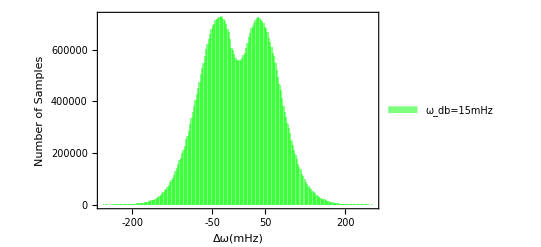

```mathematica
Histogram[{PFullFreq},200,ChartStyle->{Green},Frame->True,FrameTicks->{{{0,100000,200000,300000,400000,500000,600000,700000},None},{{{-0.004,-200},{-0.002,-100},{-0.001,-50},{0,0},{0.001,50},{0.002,100},{0.004,200}},None}}, FrameLabel->{Style["Δω(mHz)",Bold,14],Style["Number of Samples",Bold,14]},ChartLegends->Placed[{"ω_db=15mHz"},{Scaled[{0.18,0.9}], {-0.8, -0.8}}]]
```